## Elemento isoparamétrico de 3 Nodos:

### Ing. Jorge De La Cruz. Msc. Análsis por medio de Elementos Finitos.

Definiendo las coordenadas:

```mathematica
x1=0.0; y1=0.0;
x2= 4.0; y2=0.2;
x3=2.0; y3=1;
```

Graficando el elemento:

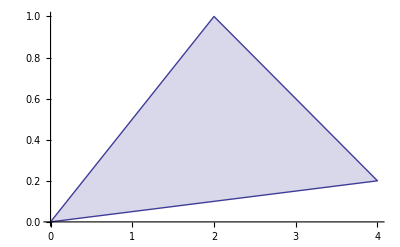

```mathematica
ListLinePlot[{{x1,y1},{x2,y2},{x3,y3},{x1,y1}},Filling->Bottom]
```

Definiendo las funciones de forma:

```mathematica
(*N1=ξ1; N2=ξ2;N3=ξ3;N33=1-ξ1-ξ2*)
```

Graficando las funciones de forma:

```mathematica
Plot3D[N33&&N33>0,{ξ1,0,1},{ξ2,1,0}]
```

-Graphics3D-

Realizando el mapeado:

```mathematica
(Matriz={{1,1,1},{x1,x2,x3},{y1,y2,y3}})//MatrixForm
(InvMatriz=Inverse[Matriz])//MatrixForm
```

(1 | 1 | 1
0. | 4. | 2.
0. | 0.2 | 1)

(1. | -0.222222 | -0.555556
0. | 0.277778 | -0.555556
0. | -0.0555556 | 1.11111)

Obteniendo el Jacobiano de la Transformación:

Ahora tenemos las derivadas inversas:

```mathematica
dξ2dx=Jinv3[[1,1]]
dξ2dy=Jinv3[[1,2]]
dξ3dx=Jinv3[[2,1]]
dξ3dy=Jinv3[[2,2]]
```

0.277778

-0.555556

-0.0555556

1.11111

Utilizando la regla de la cadena:

```mathematica
dN1dx=D[N1,ξ2]dξ2dx+D[N1,ξ3]dξ3dx
dN1dy=D[N1,ξ2]dξ2dy+D[N1,ξ3]dξ3dy
dN2dx=D[N2,ξ2]dξ2dx+D[N2,ξ3]dξ3dx
dN2dy=D[N2,ξ2]dξ2dy+D[N2,ξ3]dξ3dy
dN3dx=D[N3,ξ2]dξ2dx+D[N3,ξ3]dξ3dx
dN3dy=D[N3,ξ2]dξ2dy+D[N3,ξ3]dξ3dy
```

0.

0.

0.277778

-0.555556

-0.0555556

1.11111